Wikipedia Articles on Computational Fields

Ethan Truelove

Timothee Verdier

University of Chicago

Most representative image

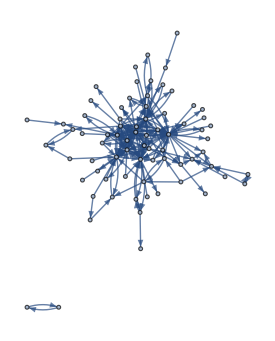
-Graphics--Graphics-

Abstract

GOAL OF THE PROJECT: Analyze Wikipedia articles on computational fields.

SUMMARY OF WORK: Looked at how articles determined to be about a given computational field (e.g. Computational physics, Computational biology, etc.) connected with one another in terms of links as well as how they differed in terms of edits made.

RESULTS AND FUTURE  WORK: There were 100 articles determined to be “computational.” Of those, 74 referenced or were referenced by at least one other article in the set. Looking at the number of total revisions on an article compared to its number of unique editors, most articles followed a linear trend of more revisions with more editors with just a couple of articles having too many or too few revisions for its given editor count. When looking at revisions over time, nearly all articles either had most edits within 1-2 months of creation or followed no substantial trend. Immediate future work would involve using the communities found and merging them with the various bar graphs to see if certain sub-groups of computational articles have any pattern in edit counts over time.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

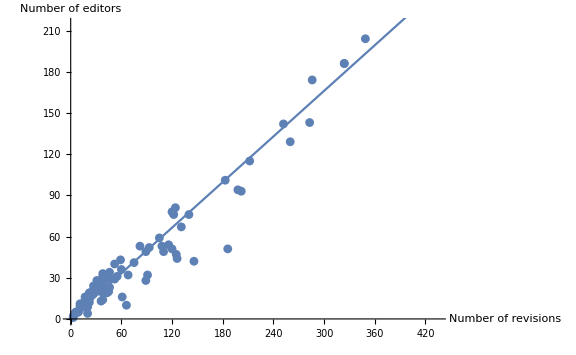
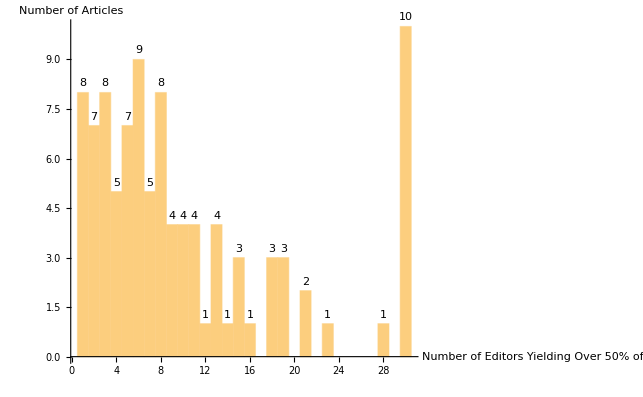
0.047+0.553x
-Graphics-



-Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

There were 100 articles determined to be “computational.” Of those, 74 referenced or were referenced by at least one other article in the set. Looking at the number of total revisions on an article compared to its number of unique editors, most articles followed a linear trend of more revisions with more editors with just a couple of articles having too many or too few revisions for its given editor count. When looking at revisions over time, nearly all articles either had most edits within 1-2 months of creation or followed no substantial trend. Immediate future work would involve using the communities found and merging them with the various bar graphs to see if certain sub-groups of computational articles have any pattern in edit counts over time.

Code

https://github.com/ethantruelove/WSS2017

## Gathering the Data

First, we need to generate a list of titles that fall into this Computational category.

```mathematica
searchlink = "https://en.wikipedia.org/w/index.php?title=Special:Search&limit=500&offset=0&profile=default&search=computational&searchToken=b9fbzhit5sdhvvts5aa00u74l";
xmlResults = Import[searchlink, "XMLObject"];
articles = Union[Flatten[Cases[xmlResults, XMLElement[_, {_, _,
	"title" -> str_String/;
		((StringMatchQ[str, StartOfString ~~"Computational"~~__])
			&&!(StringContainsQ[str, "Journal", IgnoreCase->True])),_},_]->{str}, Infinity]]];
```

The URL for the search was generated by using an Internet browser to search for the 500 top search results of “Computational”. We will then import this as an “XMLObject” where we extract just the titles of the search results. We will filter out any articles that don’t begin with “Computational” as well as articles that contain the substring “Journal” (not case sensitive). This provides us with a list of practically every Computational _ article on Wikipedia. Now we need the data.

```mathematica
TitleToInfo[articleTitle_String]:=
	AssociationMap[WikipediaData[articleTitle, #]&,
		{"ArticlePlaintext", "ExternalLinks", "ArticleContributors", "PageID",
			"SummaryPlaintext", "LanguagesList", "LinksList", "BacklinksList"}];
```

This function takes a title and adds it to an association where its value is another association with the listed fields.

```mathematica
compData = AssociationMap[TitleToInfo, articles];
```

This is a good thing to DumpSave so that excess queries can be avoided.

## Link Analysis

We will now take our list of articles and make an association where each one is a key with its corresponding information. From here, we will look at link analysis.

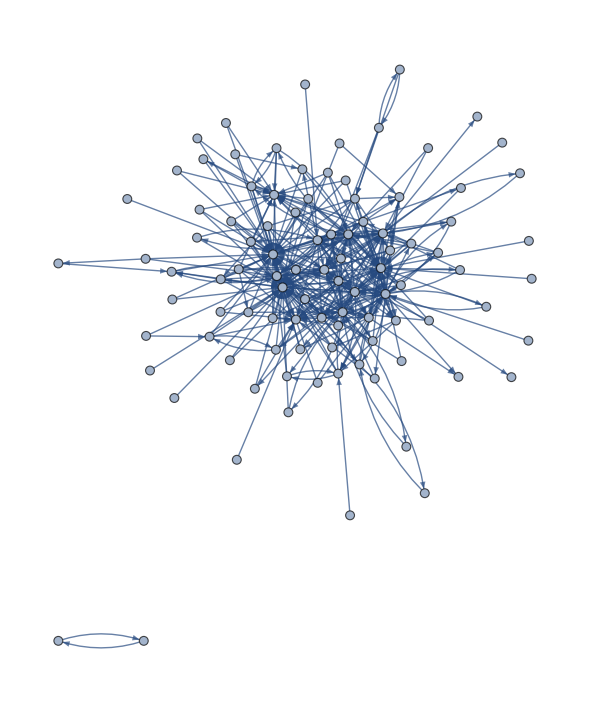

```mathematica
edgeSet = Flatten@Map[Thread, Normal@compData[[;;, "LinksList"]]];
theGraph = Graph[edgeSet];
verticesToKeep = Union[
	Keys@Select[AssociationThread[VertexList[theGraph],
	VertexInDegree[theGraph]], # ≥ 20 &
	], Keys@compData];
filteredEdges = Select[Normal@edgeSet, And[
	MemberQ[verticesToKeep, #[[1]]], MemberQ[verticesToKeep, #[[2]]]
	] &];
Graph[filteredEdges, VertexLabels -> Placed[Automatic, Tooltip]]
```

This will create a graph where an edge is defined as one article pointing to one other article that it links to. By changing the inequality on VertexInDegree, we can filter out articles that are not cited as frequently. By changing VertexInDegree to VertexOutDegree and making the inequality >= 1, we will generate a graph where vertices are just those articles found in compData as there is no link data for any articles referenced outside of this list. A list containing edges for just references between articles within our dataset can be found from:

```mathematica
compOnlyEdges = Flatten@Map[Thread, Table[Map[Thread, articles[[i]] -> Intersection[Keys[compData],
	compData[[i]][["LinksList"]]]], {i, 1, 100}]];
```

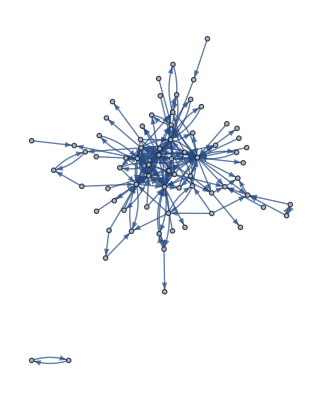

```mathematica
Graph[compOnlyEdges, VertexLabels -> Placed[Automatic, Tooltip]]
```

We can see how these articles relate with CommunityGraphPlot.

```mathematica
CommunityGraphPlot[compOnlyEdges, VertexLabels -> Placed[Automatic, Tooltip], Method -> "Hierarchical"]
```

-Graphics-

It’s important to note that this contains just 74 of the 100 articles in our set. That is because the other 26 articles neither cite nor are cited by any of the other articles in the set. We can see this from:

```mathematica
Length@Flatten@FindGraphCommunities[compOnlyEdges]
```

74

To include all articles in our set, we can add to compOnlyEdges an extra 100 edges where each edge is self-referential.

```mathematica
compOnlySingle = Union@Flatten@Append[compOnlyEdges,
	Table[Keys[compData][[i]] -> Keys[compData][[i]], {i, Length[Keys[compData]]}]];
```

```mathematica
CommunityGraphPlot[compOnlySingle, VertexLabels -> Placed[Automatic, Tooltip], Method -> "Hierarchical"]
```

-Graphics-

Now we can see all the articles, but it’s not very helpful. Instead, we can maintain a list of articles that are not cited within our 100-article set.

```mathematica
noLinks = Complement[Keys[compData], Flatten@FindGraphCommunities[compOnlyEdges]];
```

Using this,

```mathematica
CommunityGraphPlot[compOnlyEdges, VertexLabels -> Placed[Automatic, Tooltip]]
```

-Graphics-

which is the same graph as that displayed at the beginning of this section but in a different layout, we can generate groups. CommunityGraphPlot takes the groupings generated by FindGraphCommunities and plots them. By running through the methods of FindGraphCommunities, we can determine that the “Modularity” model is the best.

```mathematica
CommunityGraphPlot[compOnlyEdges,
	FindGraphCommunities[
		compOnlyEdges, Method->#
	],
	VertexLabels -> Placed[Automatic, Tooltip],
	ImageSize -> Small
]&/@{
		"Modularity",
		"Centrality",
		"CliquePercolation",
		"Hierarchical",
		"Spectral",
		"VertexMoving"
	} //Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Since we can generate the communities, we can go through and label them manually. The order they appear is based off of the number of articles in the list from longest to shortest.

```mathematica
groups = Association[
	Flatten[
		Map[
			Thread,
			Thread[
				FindGraphCommunities[compOnlyEdges]->
				{
					"Computational Chemistry Group",
					"Computational Science and Data Group",
					"Computational Biology Group",
					"Computational Thinking/Sentience Group",
					"Computational Intelligence and Economics Group",
					"Computational Physics Group",
					"Computational Complexity Group",
					"Computational Photography Group"
				}
			]
		]
	]
];
```

Now that we have groups assigned we can go through compOnlyEdges and replace each item with its corresponding group.

```mathematica
groupsEdges = Table[
	Replace[
		compOnlyEdges[[i]],
		compOnlyEdges[[i]] -> (
			groups[compOnlyEdges[[i]][[1]]] -> groups[compOnlyEdges[[i]][[2]]]
		)
	],
	{i, Length[compOnlyEdges]}
];
```

We can look at what this graph looks like.

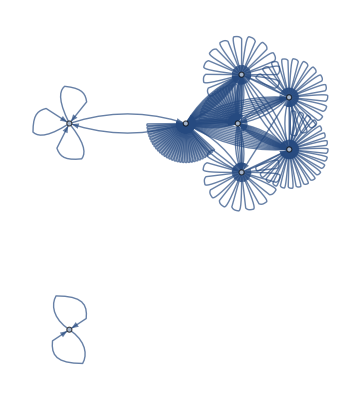

```mathematica
Graph[groupsEdges, VertexLabels -> Placed[Automatic, Tooltip]]
```

As expected, a CommunityGraphPlot using FindGraphCommunities of every model yields almost identical results as everything has already been grouped previously.

```mathematica
CommunityGraphPlot[
	groupsEdges,
	FindGraphCommunities[groupsEdges, Method -> #],
	VertexLabels -> Placed[Automatic, Tooltip],
	ImageSize -> Small
]&/@{"Modularity", "Centrality", "CliquePercolation", "Hierarchical", "Spectral"} //Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

If we want to remove the self-referential loops, we use GraphPlot instead. Note the single point that is entirely self-referential, therefore not pointing in either direction to other groups.

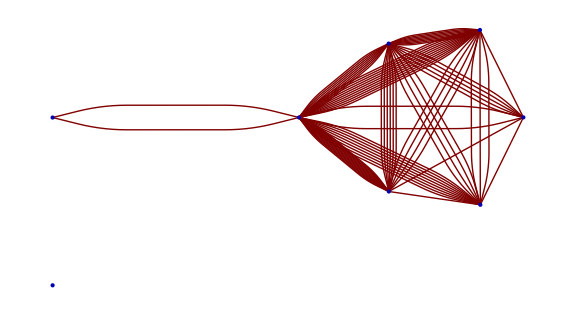

```mathematica
GraphPlot[groupsEdges, SelfLoopStyle -> None, VertexLabeling -> Tooltip, ImageSize -> Large]
```

## Edit Information

The site “tools.wmflabs.org” has much information about edit statistics of all articles on Wikipedia. To collect our data we take the template

```mathematica
template = {
	"https://tools.wmflabs.org/xtools-articleinfo/?article=",
	"&project=en.wikipedia.org"
};
```

and insert our article title in between. However, our list of articles needs to have spaces replaced by “_” before we can call the data so we must do this:

```mathematica
urlForm = Flatten@Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
```

This function will allow us to call the necessary information:

```mathematica
TitleToEdit[article_] := Block[{}, 
	(*Print[template[[1]]<> article <> template[[2]]]; *)
	Import[template[[1]]<> article <> template[[2]], "Data"]
]
```

Now we use TitleToEdit to get an association for all our articles. This is a good item to DumpSave.

```mathematica
editInfo = AssociationMap[TitleToEdit, urlForm];
```

We can use these two functions:

```mathematica
TotalRevisions[article_]:= editInfo[article][[2]][[1]][[1]][[4]][[2]]
NumEditors[article_] := N[editInfo[article][[2]][[1]][[1]][[5]][[2]]]
```

To get the total number of revisions made to an article and the unique number of editors, respectively.

```mathematica
revCount = AssociationMap[Replace[s_String :> ToExpression@StringDelete[s, ","]]@*TotalRevisions, urlForm];
editorCount = AssociationMap[NumEditors, urlForm];
```

We can now map each article to each revision count and editor count, but we need to remove commas from the strings in revCount in order to convert to an integer. One interesting metric is revisions per editor for any given article, given by revPerEditor.

```mathematica
revPerEditor=Sort[revCount / editorCount, Greater];
```

A histogram shows that revCount and editorCount are generally correlated:

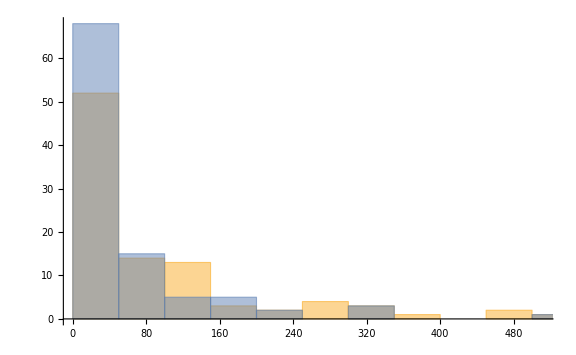

```mathematica
Histogram[{revCount, editorCount}, {50}, ImageSize -> Large, PlotRange -> Automatic]
```

But a LinePlot clearly shows that most articles follow a trend of more editors with more revisions, as might be expected.

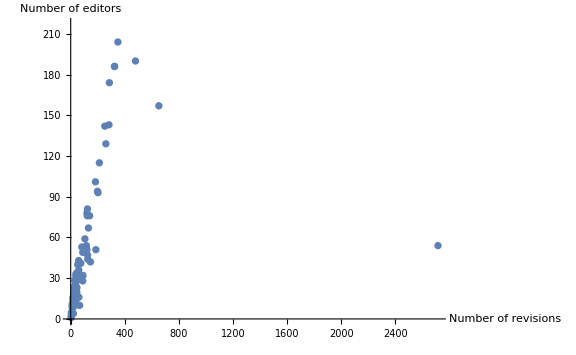

```mathematica
revEditList = Table[{revCount[[i]], editorCount[[i]]}, {i, Length[revCount]}];
ListPlot[Tooltip[revEditList], LabelingFunction -> None,
	AxesLabel -> {"Number of revisions", "Number of editors"},
	PlotRange -> {All, Automatic}, ImageSize -> Large]
```

Focusing just on articles with less than 400 revisions makes this more apparent.

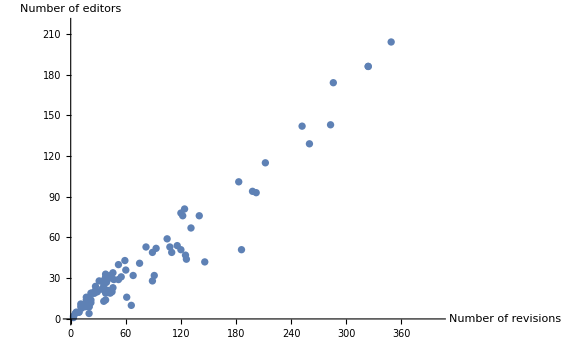

```mathematica
ListPlot[Tooltip[revEditList], LabelingFunction -> None,
	AxesLabel -> {"Number of revisions","Number of editors"},
	PlotRange -> {{0,400}, Automatic}, ImageSize -> Large]
```

## Edits Over Time

In order to see how an article has evolved over time in terms of edit activity, we will use the data to get number of edits in any given month since the article’s creation.

```mathematica
header = {"month","Number of edits","IPs","IPs %","Minor edits",
	"Minor edits %"," All edits • IPs • Minor edits"};
months = DateRange[DateObject["2001 / 01"], DateObject["Today"]];
blankDates = Table[
	{months[[i]], 0},
	{i, Length@months}
];
	
EditDates[article_] :=
	Block[{finalList,newEditInfo},
		newEditInfo = DeleteCases[Table[
			If[i ≠ header,
				i, ""
			],
			{i, editInfo[article][[2]][[6]]}
		],""];
		
		finalList = blankDates;
		For[i = 1, i ≤ Length@newEditInfo, i++,
			finalList[[i + Length@months - Length@newEditInfo - 1]][[2]] = newEditInfo[[i]][[2]]
			(*{Print[newEditInfo[[i]][[1]]],
			Print[i + Length@months - Length@newEditInfo - 1]}*)
		];
		Return[finalList]
	]
```

```mathematica
EditDatesPlot[article_] :=
	BarChart[
		EditDates[article][[All,2]],
		ChartLabels -> (
			Rotate[DateString@#, Pi/2]&/@(
				ReplacePart[EditDates[article][[All,1 ]],
					List/@Complement[Range@Length@EditDates[article],
					Range[1, Length@EditDates[article], 12]] -> ""]
			)
		), PlotLabel -> article, ImageSize -> Large
	]
```

We can once again create an association to map this, and it is also an item that is good to DumpSave.

```mathematica
editDatesGraphs = AssociationMap[EditDatesPlot, urlForm];
```

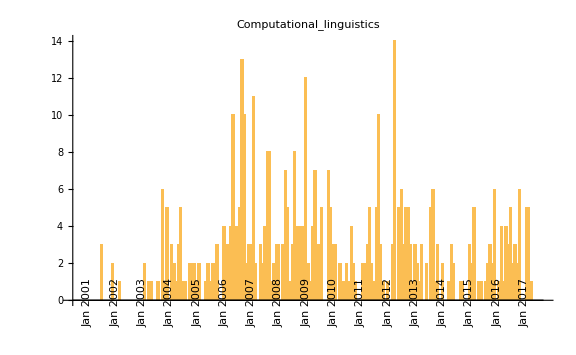

```mathematica
editDatesGraphs["Computational_linguistics"]
```

```mathematica
Manipulate[editDatesGraphs[article],{article, Keys@editDatesGraphs}]
```

## Top Editors

Now we will extract statistics on top editors on each article.

```mathematica
EditorStats[article_]:=
	If[
		Length@editInfo[article][[2]][[3]][[1]][[2;;]] ≤ 30,
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]],
			{i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]],
			{i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		]},
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, 31}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, 31}
		],
		editInfo[article][[2]][[3]][[1]][[32]]
		}
	]
```

We will then map this to each article.

```mathematica
editStats = AssociationMap[EditorStats, urlForm];
```

Here’s an example of the organization:

```mathematica
editStats["Computational_X"]
```

{{2,1},{Pleasantville,Missionedit}}

The first item in the first sublist aligns with the first item in the second sublist and so on. Make note that individualized statistics on editors is available for the top 30 contributors to each article. If there are more than 30 contributors, then a third sublist contains the additional number of editors beyond the top 30 and the cumulative number of edits those editors have made.

```mathematica
editStats["Computational_physics"]
```

{{40,8,7,6,5,4,4,4,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2},{Ema--or,92.237.25.17,Nicoguaro,JJL,Bduke,Jorgecarleitao,Djr32,81.133.28.241,FrescoBot,Fmadd,Hhhippo,David Schaich,Andrewwall,Zvelindovsky,196.10.121.2,193.198.146.227,Michael Hardy,Philippojscherer,CBM,NeonMerlin,Berg0747,Tomtzigt,Oxymoron83,AlnoktaBOT,Chobot,Robbot,GrimFang4,Tim Starling,51.37.104.97,109.66.120.41},{112 others,121,-More-}}

If we look at a specific article, we can see what part each of the top 30 editors have made within all top 30 editors.

```mathematica
PlotEditStats[article_] := PieChart[editStats[article][[1]]]
```

```mathematica
PlotEditStats["Computational_biology"]
```

-Graphics-

If we want a basic text breakdown of how editors contribute, we can use:

```mathematica
Block[{currentTotal},	
	TopEditorsText[article_] :=
		If[Length@editStats[article] == 2,
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / Total[editStats[article][[1]]] ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[ToString[i - 1] <> " of " <> 
						ToString[Length@editStats[article][[1]]] <>
						" editors of made over 50% of "
						<> ToString[Total[editStats[article][[1]]]]
						<> " total edits on the article " <> article];
					Break[]
				]
			],
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / 
					(Total[editStats[article][[1]]] + editStats[article][[3]][[2]]) ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[ToString[i - 1] <> " of " <>
						ToString[
							Length@editStats[article][[1]] + 
							ToExpression[StringTake[editStats[article][[3]][[1]],{1,-8}]]
						] <>
						" editors of made over 50% of " <> 
						ToString[Total[editStats[article][[1]]] + editStats[article][[3]][[2]]]
						<> " edits on the article " <> article];
					Break[]
				];
				If[i == Length@editStats[article][[1]],
						Return["The top 30 editors made " <> 
							ToString[100 * N@currentTotal / 
							(Total[editStats[article][[1]]] + editStats[article][[3]][[2]])]
							<> "% of " <> ToString[
							ToString[Total[editStats[article][[1]]] + 
							editStats[article][[3]][[2]]]]
							<> " edits on the article " <> article
						]
				]
			]
		]
]
```

```mathematica
TopEditorsText["Computational_complexity"]
```

6 of 11 editors of made over 50% of 11 total edits on the article Computational_complexity

Now we will make a more useful version that we can use to graph.

```mathematica
Block[{currentTotal},	
	TopEditorsFifty[article_] :=
		If[Length@editStats[article] == 2,
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / Total[editStats[article][[1]]] ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[i-1];
					Break[]
				]
			],
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / 
					(Total[editStats[article][[1]]] + editStats[article][[3]][[2]]) ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[i-1];
					Break[]
				];
				If[i == Length@editStats[article][[1]],
					Return[30]
				]
			]
		]
]
```

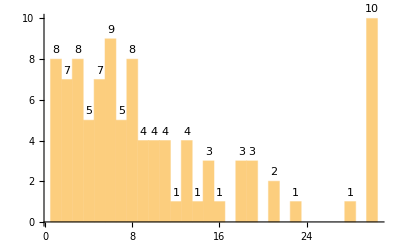

```mathematica
Histogram[AssociationMap[TopEditorsFifty, urlForm], 30, LabelingFunction -> Above]
```

Note that the category “30” is articles where the top 30 editors did not reach 50% of all contributions to an article. Data per editor beyond the top 30 editors is missing. Let’s look at how the top 30 editors contribute.

```mathematica
TopEditors[article_] :=
	If[Length@editStats[article] == 3,
		Return[
			N[
				100 * Total[editStats[article][[1]]] /
				(Total[editStats[article][[1]]] + editStats[article][[3]][[2]])
			]
		]
	]
```

For articles with 30 or less contributors, the top 30 contributors will always contribute 100% of an article’s edits. We can get the articles that have more than 30 contributors from:

```mathematica
thirtyPlus = DeleteCases[Table[If[Length@editStats[i] == 3 && editStats[i][[3]][[2]] > 0, i, ""],
	{i, urlForm}], ""];
```

Plotting it as a histogram will show show us where articles fall in terms of what percent of an article’s total edits were committed by the top 30 editors. One bin spans 5%.

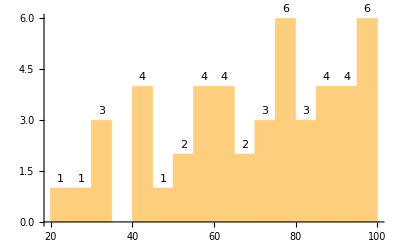

```mathematica
Histogram[AssociationMap[TopEditors, thirtyPlus], 20, LabelingFunction -> Above]
```

Written Content / Lesson Plans

N/A.

Conclusions in Detail

Many articles followed very similar patterns and did not seem to differ too much in terms of edit histories or contributors, indicating that there is are not any articles that a substantially “better” than others. As an article has more edits, it also has more editors so the ratio of editors to revisions stays approximately constant throughout, contributing to the same “quality” of article regardless of length.

All Visualizations

See code.

Data Sources Links/References

https://tools.wmflabs.org/xtools-articleinfo/

Future Directions

Redefine the set of articles when originally making compData to create the most updated list. Map groups to the different bar charts and graphs to see if there are any trends created by sub-groups of computational articles.

Background Info Links/References

N/A.

Keywords

Provide keywords as items

Wikipedia

Computational fields

Link analysis

Edit history

Other

N/A.

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```